# Convergence package

## by Ian Hinder

## Initialisation

```mathematica
<<"Convergence.m"
```

## Documentation

The Convergence package contains functions for analysing the convergence of various quantities.

## Examples

```mathematica
exact=MakeDataTable@Table[{x,1+0.1Sin[2Pi x]},{x,0,1,0.01}]
```

DataTable[...]

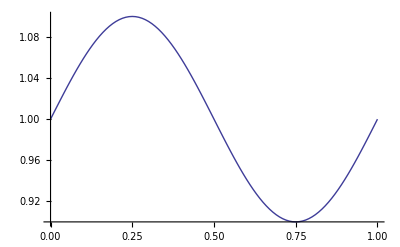

```mathematica
ListLinePlot[exact]
```

```mathematica
addErr[tb_DataTable,h_,p_]:=
MakeDataTable@Map[{#[[1]],#[[2]]+0.03Cos[2Pi #[[1]]]h^p+0.03Sin[2Pi #[[1]]]h^(p+1)}&,ToList[tb]]
```

```mathematica
{h1,h2,h3}={0.96,0.80,0.64};
```

```mathematica
order=4;
```

```mathematica
f[h1]=addErr[exact,h1,order]
```

DataTable[...]

```mathematica
f[h2]=addErr[exact,h2,order]
```

DataTable[...]

```mathematica
f[h3]=addErr[exact,h3,order]
```

DataTable[...]

```mathematica
cr4=ConvergenceMultiplier[{h1,h2,h3},4]
```

1.81843

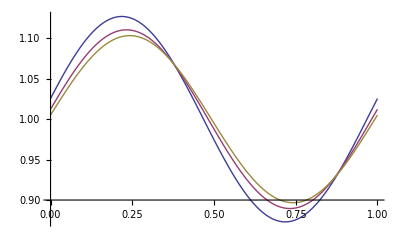

```mathematica
ListLinePlot[{f[h1],f[h2],f[h3]}]
```

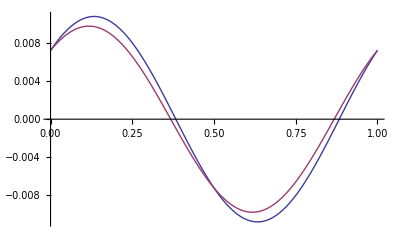

```mathematica
ListLinePlot[{(f[h1]-f[h2])/cr4,f[h2]-f[h3]}]
```

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

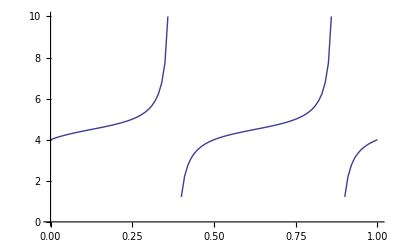

```mathematica
ListLinePlot[ConvergenceRate[{f[h1],f[h2],f[h3]},{h1,h2,h3}],PlotRange->{0,10}]
```